# Algebra

```mathematica
Today
```

Sun 22 Apr 2018

## Integers and their properties

How many different ways are there to arrange an ordinary deck of playing cards? How many different ways are there to deal 13 cards each to four players when the order of cards in each hand doesn’t matter? Basic combinatorics gives us the answers to these questions. Every introduction to combinatorics must begin with factorial and binomial functions, and this text is not an exception.

```mathematica
52!
Multinomial[13, 13, 13, 13]
```

80658175170943878571660636856403766975289505440883277824000000000000

53644737765488792839237440000

He who refuses to do arithmetic is doomed to talk nonsense. This lesson discusses the algebraic capabilities of Mathematica over integers, real numbers, polynomials and matrices. We start off with integers, simple enough that we like to think them as Trix that are for little kids, but actually turn out to have amazing computational challenges hidden in plain sight. We have already encountered factorization with the function FactorInteger that produces the list of prime factors of its argument together with their exponents. To demonstrate this function, we can factorize the big number generated by multiplying the first twenty prime numbers, each prime number furthermore raised to the power of its index in this list.

```mathematica
primePowers = FactorInteger[Product[Prime[i]^i, {i, 1, 20}]]
```

{{2,1},{3,2},{5,3},{7,4},{11,5},{13,6},{17,7},{19,8},{23,9},{29,10},{31,11},{37,12},{41,13},{43,14},{47,15},{53,16},{59,17},{61,18},{67,19},{71,20}}

For practice, we then compute the exponentiation of each pair { factor, exponent } using Map, and then Fold this list of terms into a single number to see how big this number really is.

```mathematica
Fold[Times, 1, Map[(#[[1]]^#[[2]])&, primePowers]]
```

1083774806427009584406221236421407238546165522788762542987505393755036210611448532711818140530894771729472527896811015970508099725512877197821574018280059838735575855829579501299284364939582081656305615475811160382380673325713079975983884367638043735226940688616414297203097272349757564159020880131254311489427415146259276686125250

As usual, substitution rules could produce the same result.

```mathematica
Times @@ (primePowers /. {b_, e_} -> b^e)
```

1083774806427009584406221236421407238546165522788762542987505393755036210611448532711818140530894771729472527896811015970508099725512877197821574018280059838735575855829579501299284364939582081656305615475811160382380673325713079975983884367638043735226940688616414297203097272349757564159020880131254311489427415146259276686125250

Any fool could factorize the previous number, since its prime factors are so small. Let’s try another number, this time a bit harder one, to verify that the factorization algorithm internally used by Mathematica is something a lot better than brute force testing of consecutive potential factors. The prime factors and their powers are extracts in a split second.

```mathematica
Timing[FactorInteger[Product[Prime[i]^i, {i, 100, 1000, 10}]]]
```

{0.26998,{{541,100},{601,110},{659,120},{733,130},{809,140},{863,150},{941,160},{1013,170},{1069,180},{1151,190},{1223,200},{1291,210},{1373,220},{1451,230},{1511,240},{1583,250},{1657,260},{1733,270},{1811,280},{1889,290},{1987,300},{2053,310},{2129,320},{2213,330},{2287,340},{2357,350},{2423,360},{2531,370},{2617,380},{2687,390},{2741,400},{2819,410},{2903,420},{2999,430},{3079,440},{3181,450},{3257,460},{3331,470},{3413,480},{3511,490},{3571,500},{3643,510},{3727,520},{3821,530},{3907,540},{3989,550},{4057,560},{4139,570},{4231,580},{4297,590},{4409,600},{4493,610},{4583,620},{4657,630},{4751,640},{4831,650},{4937,660},{5003,670},{5087,680},{5179,690},{5279,700},{5387,710},{5443,720},{5521,730},{5639,740},{5693,750},{5791,760},{5857,770},{5939,780},{6053,790},{6133,800},{6221,810},{6301,820},{6367,830},{6473,840},{6571,850},{6673,860},{6761,870},{6833,880},{6917,890},{6997,900},{7103,910},{7207,920},{7297,930},{7411,940},{7499,950},{7561,960},{7643,970},{7723,980},{7829,990},{7919,1000}}}

The prime factorizations of numbers of the form 2^k are not very interesting. However, inspired by the book “Seminumerical Algorithms” by Donald E. Knuth, we can instead tabulate the prime factorizations of 2^k+1 and 2^k-1, over some suitable values of k. To make sure that Mathematica doesn’t immediately simplify the product back into the original number, we convert each exponentiation into superscript, and then use a substitution rule to get rid of the redundant exponents that equal one. The function Riffle is then used to riffle the symbol × between each individual term, and the resulting list is converted into a Row for display purposes.

```mathematica
productform[n_?PrimeQ] := n;
productform[n_] := Row[Riffle[Map[(Superscript[#[[1]],#[[2]]])&, FactorInteger[n]] /. Superscript[a_, 1] -> a, {"×"}]];
TableForm[Table[{k, productform[2^k-1], productform[2^k+1]}, {k, 15, 33}], TableHeadings->{None, {k, Superscript[2, k]-1, Superscript[2, k] + 1}}]
```

k | -1+2^k | 1+2^k
15 | 7×31×151 | 3^2×11×331
16 | 3×5×17×257 | 65537
17 | 131071 | 3×43691
18 | 3^3×7×19×73 | 5×13×37×109
19 | 524287 | 3×174763
20 | 3×5^2×11×31×41 | 17×61681
21 | 7^2×127×337 | 3^2×43×5419
22 | 3×23×89×683 | 5×397×2113
23 | 47×178481 | 3×2796203
24 | 3^2×5×7×13×17×241 | 97×257×673
25 | 31×601×1801 | 3×11×251×4051
26 | 3×2731×8191 | 5×53×157×1613
27 | 7×73×262657 | 3^4×19×87211
28 | 3×5×29×43×113×127 | 17×15790321
29 | 233×1103×2089 | 3×59×3033169
30 | 3^2×7×11×31×151×331 | 5^2×13×41×61×1321
31 | 2147483647 | 3×715827883
32 | 3×5×17×257×65537 | 641×6700417
33 | 7×23×89×599479 | 3^2×67×683×20857

The functions DigitCount and IntegerDigits can be used to extract the individual digits of an integer, in any base. For example, how many times does the digit 7 appear altogether in the base-10 representations of the first n prime numbers up to 10,000?

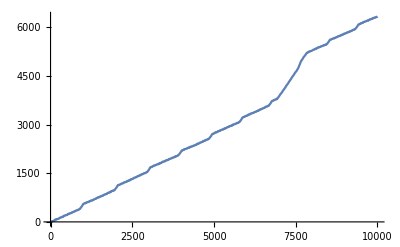

```mathematica
ListLinePlot[Accumulate[Table[DigitCount[Prime[i], 10, 7], {i, 1, 10000}]]]
```

For working in specifically base 2 where integers are expressed in binary numbers, as most computers internally do, there are special functions BitAnd, BitOr, BitXor and BitNot to perform bitwise arithmetic. The bitwise exclusive or is perhaps the most interesting of all bitwise functions, with many interesting applications.

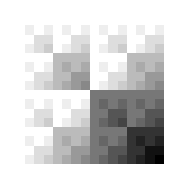
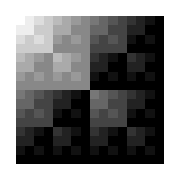
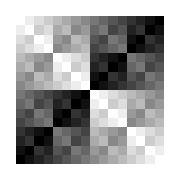

```mathematica
Row[Table[ArrayPlot[Table[f[a, b], {a, 0, 15}, {b ,0, 15}],  ImageSize -> Small], {f, {BitAnd, BitOr, BitXor}}]]
```

One-time pad must surely be the most famous application of the bitwise exclusive or. The one-time pad scheme is in principle a completely unbreakable encryption scheme whose only weakness is its inherent requirement that the communicating parties must have been previously together to generate identical random pad. Furthermore, the pad has to be generated with some cryptographically secure random number generation method so that the enemy could not just brute force through every possible seed value of the silly random number generator, generate the pad for each seed and check if each pad produces something that resembles natural language.

To encrypt the plaintext message, the sender computes the bitwise exclusive or of the plaintext and the pad. To decrypt the message, the receiver performs the exact same computation to the ciphertext and his copy of the pad. The two applications of the exclusive or always cancel each other out, leaving only the original plaintext message. As long as the pad is generated randomly and is not reused (after all, this scheme is called “One-time pad” for a good reason), not even one bit of information can be mathematically extracted from the intercepted ciphertext, at least without using some rubber hose and bamboo sticks on the captured sender, but in that situation, you wouldn’t need the intercepted message anyway.

```mathematica
pad = RandomInteger[{0, 2^16-1}, 100];
plaintext = "Hello there, world! How are you on this fine sunny day?"
chars = Flatten[ToCharacterCode[Characters[plaintext]]];
cipher = BitXor[chars, Take[pad, Length[chars]]];
StringJoin[FromCharacterCode[cipher]]
received = StringJoin[FromCharacterCode[BitXor[cipher, Take[pad, Length[chars]]]]]
```

Hello there, world! How are you on this fine sunny day?

㭍臭དྷ같齰਷뎴鼿▨ꁳ눼桄일꟠:d930oㅄ␼᧱잓ᗤ뮵꿏쾫瘺ý곥쪕э䔉뛾ᗆﲸ嘼ꓺ殭ᷯ⟨쀡颞둎胮痶ꣻ隭都㑀雁ﵕ혛㤡

Hello there, world! How are you on this fine sunny day?

Solving or optimizing a system of equations with the familiar Mathematica functions can be restricted to the integer domain. This can help ensure that the solution set is finite.

```mathematica
Solve[{x^2 + y == 20, x < y}, {x, y}, Integers]
```

{{x→-4,y→4},{x→-3,y→11},{x→-2,y→16},{x→-1,y→19},{x→0,y→20},{x→1,y→19},{x→2,y→16},{x→3,y→11}}

```mathematica
Maximize[{Sqrt[x] + Sqrt[(15 - x)], x > 0, x  < 10}, x, Integers]
```

{2 √2+√7,{x→7}}

```mathematica
Maximize[{Sqrt[x] + Sqrt[(15 - x)], x > 0, x  < 10}, x]
```

{√30,{x→15/2}}

Many common combinatorial functions of integers and the properties of these functions are, of course, already defined in their general symbolic form.

```mathematica
{ Binomial[10, 3], Fibonacci[10], StirlingS1[10, 3], StirlingS2[10, 3]}
```

{120,55,-1172700,9330}

The Z-transform can be used to analyze the properties of any integer series, especially those that are infinite but the Z-transform gives them a finite closed-form representation. Of course Mathematica knows plenty of the results of the transformations for various functions. The textbook example of this technique is to use the Z-transform to derive a closed-form formula for Fibonacci numbers. The necessary summation and partial fractions drudgery is done automatically behind the scenes, and out pops a very strange-looking formula chock full of powers of irrational numbers from which it is not immediately obvious that it will always produce an integer. And yet it does, and precisely the Fibonacci numbers.

```mathematica
ZTransform[Fibonacci[i], i, z]
```

z/(-1-z+z^2)

```mathematica
InverseZTransform[%, z, i]
```

(-(1/2 (1-√5))^i+(1/2 (1+√5))^i)/(√5)

```mathematica
Table[% /. i-> n, {n, 1, 20}] // FullSimplify
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

It would be rather strange if Mathematica did not know the binomial theorem. So of course it does.

```mathematica
Sum[Binomial[n, k] a^(n-k)b^k, {k, 0, n}]
```

(a+b)^n

Integers often occur in recursive equations that we would like to express explicitly in a closed nonrecursive form. Mathematica can solve such equations in many ways, all packed under the hood of the small but powerful function RSolve. The series that is found as a solution does not need to consist of only integers, although recursions that represent the combinatorial counting of some quantity will always do so.

```mathematica
RSolve[{a[n+1] == a[n] * 2, a[0] == 1}, a[n], n]
```

{{a[n]→2^n}}

```mathematica
RSolve[{a[n+1] == a[n] + 2 a[n-1], a[0] == 1, a[1] == 1}, a[n], n]
```

{{a[n]→1/3 ((-1)^n+2^(1+n))}}

RSolve is handy in analysing the running time t[n] for some recursive algorithm. For example, suppose that some algorithm, when executed for a list of n elements, performs a linear pass through that list and spends c time units for each element, after which it calls itself recursively for each third of the list. As a function of the list length n, what is the running time of this recursion?

```mathematica
RSolve[{t[n] == c n + 3t[n/3], t[1] == 1}, t[n], n]
```

{{t[n]→n (1+(c Log[n])/Log[3])}}

RSolve can handle any such recursion whose asymptotic behaviour would otherwise be estimated with the Master theorem.

```mathematica
RSolve[{a[n] == 8a[n/2] + 1000 n^2, a[1] ==1}, a[n], n]
```

{{a[n]→n^2 (-1000+1001 n)}}

If you simply have a series of integer values given to you as a puzzle (in the sense of IQ tests), perhaps by a group of slimy aliens from the outer space who challenge you to solve it so that they agree not to destroy humanity, giving you ample motivation to investigate what process might have generated this series, FindSequenceFunction might be able to “solve” this problem by finding a simple function that perfectly fits the series.

```mathematica
Table[2^n - n^2, {n, 1, 10}]
```

{1,0,-1,0,7,28,79,192,431,924}

```mathematica
FindSequenceFunction[%,n]
```

2^n-n^2

Since there are always infinitely many essentially different possible solutions to any such problem, this function will do the right thing and simply give up unless the sequence is long and clear so that some solution shines through brightly enough. One should not extrapolate wildly from insufficient data.

```mathematica
FindSequenceFunction[{1,2,3,4,10}]
```

FindSequenceFunction[{1,2,3,4,10}]

## Polynomial algebra

Polynomials, either univariate or multivariate, offer many more interesting possibilities for symbolic computations than the bare integers. The individual terms of a polynomial can be combined and factored into many mathematically equivalent forms. The symbolic manipulation of polynomial expressions is performed regardless of the semantic meaning of the symbols you use in them. This is mathematically correct as long as it can be assumed that addition and multiplication satisfy certain axiomatic properties when applied to those symbols.

```mathematica
Expand[(x+1)^10 - 5]
```

-4+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
Factor[♛ ^10 - 1]
```

(-1+♛) (1+♛) (1-♛+♛^2-♛^3+♛^4) (1+♛+♛^2+♛^3+♛^4)

```mathematica
Factor[x^10-1, Modulus -> 2]
```

(1+x)^2 (1+x+x^2+x^3+x^4)^2

```mathematica
Together[1/(x+1) + 3x / (x^2 - 2) - 7 / (x + 4)]
```

-(3 (-2-8 x-4 x^2+x^3))/((1+x) (4+x) (-2+x^2))

```mathematica
Apart[%]
```

1/(1+x)-7/(4+x)+(3 x)/(-2+x^2)

```mathematica
FullSimplify[%]
```

1/(1+x)-7/(4+x)+(3 x)/(-2+x^2)

```mathematica
Expand[(x+2y+1)^4]
```

1+4 x+6 x^2+4 x^3+x^4+8 y+24 x y+24 x^2 y+8 x^3 y+24 y^2+48 x y^2+24 x^2 y^2+32 y^3+32 x y^3+16 y^4

```mathematica
Collect[%, x]
```

1+x^4+8 y+24 y^2+32 y^3+16 y^4+x^3 (4+8 y)+x^2 (6+24 y+24 y^2)+x (4+24 y+48 y^2+32 y^3)

```mathematica
PolynomialGCD[x^4-2x^3 + 2, 4x^5 - 8x]
```

1

```mathematica
PolynomialLCM[x^4-2x^3 + 2, 4x^5 - 8x]
```

(2-2 x^3+x^4) (-8 x+4 x^5)

```mathematica
CoefficientList[4x^3 + 7x - 9, x]
```

{-9,7,0,4}

```mathematica
CoefficientRules[4x^3 + 7 x - 9, x]
```

{{3}→4,{1}→7,{0}→-9}

The functions for handling and transforming expressions that consist of trigonometric functions are analogous to those that handle polynomials. Just like for polynomials, many equivalent representations and forms are possible for functions that involve transcendental trigonometric functions. For example, we would sometimes like to get rid of those pesky coefficients inside the trigonometric functions, and express the formula using only sines and cosines of the bare x.

```mathematica
TrigExpand[Sin[2x]Cos[3x]]
```

-Sin[x]/2+5/2 Cos[x]^4 Sin[x]-5 Cos[x]^2 Sin[x]^3+Sin[x]^5/2

```mathematica
TrigFactor[%]
```

2 Cos[x]^2 (-1+2 Cos[2 x]) Sin[x]

```mathematica
TrigReduce[%]
```

1/2 (-Sin[x]+Sin[5 x])

```mathematica
TrigToExp[%]
```

-1/4 ⅈ ⅇ^(-ⅈ x)+1/4 ⅈ ⅇ^(ⅈ x)+1/4 ⅈ ⅇ^(-5 ⅈ x)-1/4 ⅈ ⅇ^(5 ⅈ x)

As the next plot illustrates visually, all of the above formulas are equivalent in the sense that they produce the same results for the same parameter values. In mathematics and computer programming, all functions are black boxes in that only the result that they generate matters, not the actual steps needed to produce it.

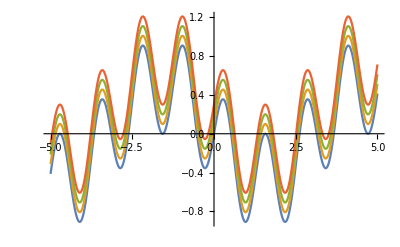

```mathematica
Plot[{%, %% + 0.1, %%% + 0.2,%%%% + 0.3}, {x, -5, 5}]
```

As is well known in mathematics, there are no general analytical formulas to solve polynomial equations that are of the order five or higher. Exact symbolic solutions can still be found in many special cases, and Mathematica will usually find them if they are known to humanity to begin with. In the absense of such solutions, any equation can always be approximated numerically. The fastest way to find one approximate numerical solution is to use the function FindRoot. For finding some local minimum or a local maximum that does not need to be global, the analogous functions are FindMinimum and FindMaximum. (The naming convention of Mathematica functions is to use the prefix Find to name all functions that only need to find the first solution from however many there really exist.)

These functions can be given an optional EvaluationMonitor, a callback function that the function executes every time it makes a move. This has no effect on the result, but allows us to watch what is going on inside the function. In addition to the equation to solve, these functions also need you to give them an initial “guess” to tell them from where to start looking for a solution. In the case of multiple or infinite solutions, this guess determines which solution you will eventually end up with. (That, and your choice of search method from the available options.) To demonstrate all this, the next transcendental equation does indeed have a symbolic solution for its infinite number of roots, but hey, if you only need one of them...

```mathematica
FindRoot[Cos[x^2] == 1/2, {x, 1},  EvaluationMonitor :> Print["x is ", x ]]
```

x is 1.

x is 1.02395

x is 1.02333

x is 1.02333

x is 1.02333

{x→1.02333}

The solution set, although infinite, can be expressed in a finite form by introducing additional parameters, canonically named using the subscripted letter c. Mathematica does this automatically using the capital letter C to ensure that this name doesn’t clash with the symbols that you use in your program. Remember, every time you capitalize your symbol name, you take a chance that it will clash with some built-in function. Even if such a function doesn’t exist yet, the next version of Mathematica might have such a function.

```mathematica
Solve[Cos[x^2] == 1/2]
```

{{x→ConditionalExpression[-√(-π/3+2 π C[1]),C[1]∈Integers]},{x→ConditionalExpression[√(-π/3+2 π C[1]),C[1]∈Integers]},{x→ConditionalExpression[-√(π/3+2 π C[1]),C[1]∈Integers]},{x→ConditionalExpression[√(π/3+2 π C[1]),C[1]∈Integers]}}

```mathematica
NSolve[Cos[x^2] == 1/2]
```

{{x→ConditionalExpression[-1. √(-1.0472+6.28319 C[1]),C[1]∈Integers]},{x→ConditionalExpression[√(-1.0472+6.28319 C[1]),C[1]∈Integers]},{x→ConditionalExpression[-1. √(1.0472+6.28319 C[1]),C[1]∈Integers]},{x→ConditionalExpression[√(1.0472+6.28319 C[1]),C[1]∈Integers]}}

Sometimes a solution simply does not exist for the given system of equations, so the solution returned is the empty set.

```mathematica
Solve[{x^2 + y^2 == 99}, {x, y}, Integers]
```

{}

Even when exact symbolic solutions don’t exist for a polynomial equation of order five or higher, we can still extract a fully symbolic answer that consists of Root formulas of that polynomial. These roots can then ride along further symbolic computations where they hopefully either vanish from the equation or allow simplification with additional information available later, and if not, be later converted to approximate numerical solutions. As the fundamental theorem of algebra teaches us, any non-constant polynomial of order n has exactly n roots, some of which are complex numbers.

```mathematica
Solve[4x^7 + 3x^3 - 1 == 0, x]
```

{{x→Root[-1+3 #1^3+4 #1^7&,1]},{x→Root[-1+3 #1^3+4 #1^7&,2]},{x→Root[-1+3 #1^3+4 #1^7&,3]},{x→Root[-1+3 #1^3+4 #1^7&,4]},{x→Root[-1+3 #1^3+4 #1^7&,5]},{x→Root[-1+3 #1^3+4 #1^7&,6]},{x→Root[-1+3 #1^3+4 #1^7&,7]}}

```mathematica
N[%, 20]
```

{{x→0.6465939857476875874},{x→-0.71154352476882013989-0.5636812817670074783 ⅈ},{x→-0.71154352476882013989+0.5636812817670074783 ⅈ},{x→-0.2833071353771691308-0.63029702872181860669 ⅈ},{x→-0.2833071353771691308+0.63029702872181860669 ⅈ},{x→0.671553667272145477-0.72909012336967819764 ⅈ},{x→0.671553667272145477+0.72909012336967819764 ⅈ}}

The function Reduce is similar to Solve, but is used to simplify systems of equations and inequalities with respect to some set of variables. The more assumptions about the variables and their domains you make, the more this function can potentially tell you about its solutions.

```mathematica
Reduce[Log[x] > 100, x]
```

x>ⅇ^100

```mathematica
Reduce[x^3 - 2 x y^2 == 1, {x, y}, Integers]
```

(x==-1&&y==-1)||(x==-1&&y==1)||(x==1&&y==0)

```mathematica
Reduce[x^3 - 2 x y^2 == 1, {x, y}, Modulus -> 5]
```

(x==1&&y==0)||(x==3&&y==1)||(x==3&&y==4)||(x==4&&y==1)||(x==4&&y==4)

The reduction produces one formula where the logical connectives && and || are shorthand infix forms for Boolean functions And and Or, respectively. This strange syntax is quite common in major programming languages, even though it really isn’t the clearest, but it lives on even in Mathematica for historical reasons. When you type in formulas, you can use the mathematical writing symbols ∧ and ∨ in their place.

Surely everyone has heard the maxim that assuming things makes an “ass” out of “u” and “me”. Even so, the function Refine can simplify the formula according to what we are Assuming about the world around it. For example, the square root of a square can be simplified only if we assume that we are dealing with a positive quantity.

```mathematica
Assuming[x>0, Refine[Sqrt[x^2]]]
```

x

```mathematica
Refine[Sqrt[x^2]]
```

√(x^2)

Systems of inequalities generally have an infinite number of solutions. The function FindInstance does exactly what it says on the tin, finds one combination of values for the unknown variables that together satisfy all constraints of the problem. In the case of multiple or even infinite solutions, again there is no telling beforehand which particular instance you get. So you will get what you get and you will like it, but what you get might be different in the next version of Mathematica, or even when the same version is run on a different computer architecture. For this reason, you can’t argue the correctness of any Mathematica program with some handwaving assumption that this function will always first find some particular instance for the given problem.

```mathematica
FindInstance[{x^2 - x y == 10, x > 0, y > 0}, {x, y}, Integers ]
```

{{x→5,y→3}}

```mathematica
FindInstance[{x^ (y-6) == (x+y)^2}, {x, y}]
```

{{x→Root[{(-1517/100-(39 ⅈ)/25)+#1^(-99/10-ⅈ/5)+(39/5+(2 ⅈ)/5) #1-#1^2&,3.898902906091620445422325125888771896397543331303429396+0.200451566824147340996093053906524906769783256629103086 ⅈ}],y→-39/10-ⅈ/5}}

Curve fitting is an important application of polynomials and other elementary functions. The general purpose function Fit gets two arguments, the first one being the list of data points to fit the curve into, and the second the list of functions that Fit is allowed to combine together to approximate the data. Usually these functions are simple polynomials, as they would always have to be in lesser systems than Mathematica, but in principle they could be anything, which makes this function more powerful than other systems that can only fit polynomials. Fit will then find the linear combination of these allowed functions that fits the data points the best in the least squares error sense. The next example generates a series of data points by adding random noise to a function, and then tries to approximate the result using either polynomials of degree of three, cosines with four different frequencies, and last a wacky pack of Fibonacci, Lucas and Euler Phi integer functions.

```mathematica
testdata = Table[{i, 3Sqrt[i] - 2Sin[i]+ RandomReal[{-1, +1}]}, {i, 0, 20}]
f1 = Fit[testdata, {1, x, x^2, x^3}, x]
f2 = Fit[testdata, {1, Cos[x], Cos[2x], Cos[3x]}, x]
f3 = Fit[testdata, {Fibonacci[Floor[x]], LucasL[Floor[x]], EulerPhi[Floor[x]]}, x]
```

{{0,0.633347},{1,1.58342},{2,3.37351},{3,5.04246},{4,7.35449},{5,8.61638},{6,8.06659},{7,5.67425},{8,6.84072},{9,9.06789},{10,11.159},{11,11.8565},{12,12.0794},{13,10.33},{14,8.4965},{15,10.201},{16,12.7891},{17,13.8887},{18,13.7863},{19,13.5175},{20,12.0728}}

0.730262+1.62352 x-0.0925374 x^2+0.00217094 x^3

8.90058-0.269766 Cos[x]-0.152578 Cos[2 x]-0.385261 Cos[3 x]

1.11531 EulerPhi[Floor[x]]-0.954819 Fibonacci[Floor[x]]+0.427082 LucasL[Floor[x]]

Plotting the curves around the red data points shows the way that they try to approximate the points. Note that none of the interpolated curves perfectly interpolate all the data points.

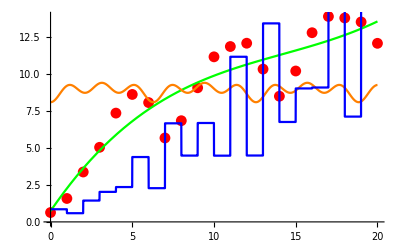

```mathematica
Show[ListPlot[testdata, PlotStyle-> Red], Plot[f1,{x, 0, 20}, PlotStyle -> Green],  Plot[f2,{x, 0, 20}, PlotStyle -> Orange], Plot[f3,{x, 0, 20}, PlotStyle -> Blue]]
```

As polynomial algebra teaches us, for any given n distinct data points there always exists exactly one unique polynomial of the degree n - 1 that fits these data points exactly. However, if n is more than what you can count with your fingers, using one big polynomial to try to capture this entire set of data points doesn’t make much sense in practice because of Runge’s phenomenon. As the next plot demonstrates, this unique polynomial will in nearly all cases behave nice and smooth in the middle of the data, but shoot wildly up and down at the extremal points of the data.

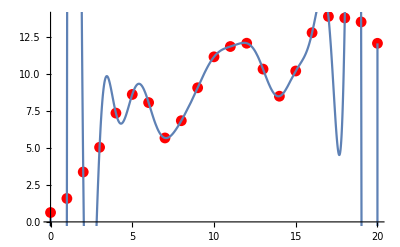

```mathematica
f3 = InterpolatingPolynomial[testdata, x];
Show[ListPlot[testdata, PlotStyle->Red], Plot[f3, {x, 0, 20}]]
```

A curve that fits the given data points perfectly can be constructed with Interpolation. Under the hood of this fitting mechanism, such interpolating function is constructed piecewise from splines or other functions that behave better than those high-order polynomials that try to capture the entire data into one polynomial. To ensure that the pieces have no visible discontinuities in their connection points, the construction of the pieces requires that the derivatives of consecutive pieces must also be equal in the connection point. These derivatives are computed from control points that the method automatically generates between the known data points.

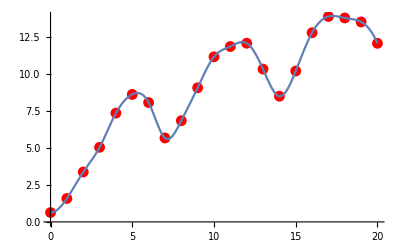

```mathematica
f4 = Interpolation[testdata, Method-> "Spline"];
Show[ListPlot[testdata, PlotStyle->Red], Plot[f4[x], {x, 0, 20}]]
```

Whenever you plot some function or a data set graphically, Mathematica will internally generate a smooth interpolating function and then actually display the interpolation instead of “real” curve that was sampled in a finite set of points. This allows you to zoom, rotate and move the curve every which way but loose, and the curve remains smooth instead of becoming ugly and pixellated as would happen in zooming a pixel raster.

For even more general fitting problems for possibly huge data sets measured from some real world problem domain, Mathematica has two high-level machine learning functions Classify and Predict that pack a lot of punch under the hood. Given the training data as a list of elements and their intended classifications so that the number of classes is much smaller than the number of elements, Classify will analyze this training data to build a classifier for unseen elements. The function Predict will do the same to interpolate a function that can have as many different results as it has elements. Internally, both functions have a ton of options and method to decide what particular machine learning approach to use, if you want to fiddle with this perhaps to compare the different approaches. Because these functions are intended to be used in situations where the training data consists of noisy samples from some complex problem domain, to avoid overfitting, the models that are internally built by these functions generally do not even attempt to intersect all the data points of the training set. 

Here a simple and completely artificial example of predicting the logarithm of a positive integer from a hundred training samples. This is not a difficult problem to classify for any reasonable feature-looking machine learning algorithm, so the classifier should get quite a few of our validation samples right. And indeed it does.

```mathematica
datac = Table[elem = RandomInteger[1000000]; elem -> Floor[Log[elem]], {i, 1, 100}];
classifier = Classify[datac];
datacv =  Table[elem = RandomInteger[1000000]; elem , {i, 1, 100}];
Total[Map[(Boole[classifier[#] ==Floor[Log[#]]])&, datacv]]
```

92

```mathematica
ClassifierInformation[classifier]
```

Classifier information
Method | Random forest
Number of classes | 7
Number of features | 1
Number of training examples | 100
Number of extracted features | 1
Number of trees | 10

To demonstrate Predict, let us generate some training data by adding random noise to a simple function, and see if Predict can learn the underlying smooth function under that noise. The neural network learning algorithm chosen seems to work quite well a function that simple.

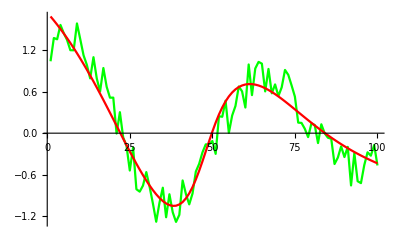

```mathematica
ClearAll[datap, predictor, datapv]
datap = Table[i -> Sin[i/10] + Cos[i/9] +RandomReal[{-0.3, +0.3}], {i, 1, 100}];
predictor =Predict[datap, Method -> "NeuralNetwork"];
datapv = Table[predictor[i], {i, 1, 100}];
Show[ ListLinePlot[Map[(#[[2]])&, datap], PlotStyle->Green], ListLinePlot[datapv, PlotStyle -> Red],PlotRange ->Automatic]
```

```mathematica
PredictorInformation[predictor]
```

Predictor information
Method | Neural network
Number of features | 1
Number of training examples | 100
Number of extracted features | 1
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,33
Hidden layer activation functions | ,,TanhTanh

## Matrix algebra

In Mathematica, matrices are implemented as lists of lists with the additional constraint that each element list must have the same number of elements. In other words, a matrix is now allowed to be ragged or have gaps, unlike a more general list of lists. An arbitrary matrix can always be created with the function Table using two index variables, or the hard way by explicitly listing its elements, in case that Mathematica doesn’t already have a built-in function for numerous important families of special types of matrices that often occur in practical problems.

For example, let us tabulate the approximations of the probabilities of the famous birthday paradox problem, but to make this more interesting, do this calculation for all of the eight planets of the solar system! (A program can never be too general-purpose!) The birthday paradox asks the probability that in a set of n randomly chosen people, there are no two people who share the same birth date. The full probability formula becomes a bit hairy (although Mathematica’s unlimited precision calculations can handle it easily), but it can still be approximated close enough for government work with a much simpler formula. Since the function EntityValue has the attribute Listable, we can apply it to a list of entities exactly the same as to just one entity.

```mathematica
planets = PlanetData[]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
yearlens = EntityValue[planets, "OrbitPeriod"]
```

{87.96926,224.7008,365.25636,1.8808476,11.862615,29.447498,84.016846,164.79132}

Starting from version 9, Mathetica is able to internally represent physical quantities and units, and perform and reason about the relationships and conversions between them. Internally, numbers with quantities are stored as expressions with the head Quantity, the expression itself containing the numerical part and the unit. Conversion to a desired unit takes place easily with the function UnitConvert. The unit part can be stripped away from the compound quantity with the function QuantityMagnitude.

```mathematica
% // FullForm
```

List[Quantity[87.96926,"Days"],Quantity[224.7008,"Days"],Quantity[365.25636,"Days"],Quantity[1.8808476,"JulianYears"],Quantity[11.862615,"JulianYears"],Quantity[29.447498,"JulianYears"],Quantity[84.016846,"JulianYears"],Quantity[164.79132,"JulianYears"]]

The following table shows the probability of some two people within the group not having the same birthday, the number of people in the group on the vertical column, and the planet that they were born on the horizontal rows.

```mathematica
yearlens = Map[QuantityMagnitude[UnitConvert[#, "Days"]]&,yearlens];
probs = Table[N[E^(-m(m-1)/(2n)), 3], {m, 15, 30},{n, yearlens}];
TableForm[probs, TableHeadings->{Range[15, 30], EntityValue[planets, "Name"]}]
```

| Mercury | Venus | Earth | Mars | Jupiter | Saturn | Uranus | Neptune
15 | 0.303 | 0.627 | 0.75 | 0.858 | 0.976 | 0.99 | 0.997 | 0.998
16 | 0.256 | 0.586 | 0.72 | 0.84 | 0.973 | 0.989 | 0.996 | 0.998
17 | 0.213 | 0.546 | 0.689 | 0.82 | 0.969 | 0.987 | 0.996 | 0.998
18 | 0.176 | 0.506 | 0.658 | 0.8 | 0.965 | 0.986 | 0.995 | 0.997
19 | 0.143 | 0.467 | 0.626 | 0.78 | 0.961 | 0.984 | 0.994 | 0.997
20 | 0.115 | 0.429 | 0.594 | 0.758 | 0.957 | 0.982 | 0.994 | 0.997
21 | 0.0919 | 0.393 | 0.563 | 0.737 | 0.953 | 0.981 | 0.993 | 0.997
22 | 0.0724 | 0.358 | 0.531 | 0.714 | 0.948 | 0.979 | 0.993 | 0.996
23 | 0.0564 | 0.324 | 0.5 | 0.692 | 0.943 | 0.977 | 0.992 | 0.996
24 | 0.0434 | 0.293 | 0.47 | 0.669 | 0.938 | 0.975 | 0.991 | 0.995
25 | 0.033 | 0.263 | 0.44 | 0.646 | 0.933 | 0.972 | 0.99 | 0.995
26 | 0.0249 | 0.235 | 0.411 | 0.623 | 0.928 | 0.97 | 0.989 | 0.995
27 | 0.0185 | 0.21 | 0.383 | 0.6 | 0.922 | 0.968 | 0.989 | 0.994
28 | 0.0136 | 0.186 | 0.355 | 0.577 | 0.916 | 0.965 | 0.988 | 0.994
29 | 0.0099 | 0.164 | 0.329 | 0.554 | 0.911 | 0.963 | 0.987 | 0.993
30 | 0.00712 | 0.144 | 0.304 | 0.531 | 0.904 | 0.96 | 0.986 | 0.993

As you can see from the table, on Earth you need only 23 randomly chosen Terrans to have a roughly a coin toss chance of having at least two of these people sharing the same birth date. This famous result seems counterintuitive, since there are 365 days in a year, and 23 just feels like such as small number compared to 365. However, from 23 people it is possible can form 253 separate pairs, and as long as there exists one pair with the same birthday, you win. On the planet Uranus where the year lasts over 30,000 Earth days, 30 randomly chosen Uranians are not very likely to have a pair who share a birthday, but the probability of this happening is still surprisingly large, 0.012. On the planet Mercury where the year has only 88 Earth days, a group of mere fifteen Mercurians already has about 70% chance of at least one shared birthday.

The birthday paradox has important consequences in implementing various hash table data structures that represent dynamic sets of elements whose contents can change over time by element additions and deletions. Hashed data structures never compare the order of two elements to see which one is larger and keep the data organized that way, but instead they consist of slots in which elements are added one at the time. The slots are kept in a linear table, and the slot number that each element x is stored in is computed using some hash function that converts the element x into an integer index in some suitably rapid but scrambly fashion. When adding or searching for some element x in the table, you first calculate its slot number Hash[x] and then look only in that slot, because that is the only place where the element x can be. However, the fly in this nifty little ointment is that because of the previous birthday paradox, hash collisions where two elements hash into the same slot become well nigh inevitable, even if the number of slots is large compared to the number of elements in the set. Every hashed data structure must therefore implement some kind of collision resolution scheme to resolve what happens if two elements try to enter the same slot.

Mathematica actually comes with a built-in hash function Hash that can be applied to any expression. Under the hood, this function packs a wallop of many good implementations of various cryptographic hash functions that you can choose from with the optional second argument. The hash of any expression is guaranteed to be a positive integer, which are in this context usually expressed in the hexadecimal base 16 where the letters from a to f stand for the missing digits from 10 to 15. The function IntegerString can convert its argument integer to any base.

```mathematica
IntegerString[Hash[ExampleData[{"Text", "AliceInWonderland"}], "SHA256"], 16]
IntegerString[Hash[2+2, "MD5"], 16]
```

55d6a208a049850fea4006ca98b981198ac9345fd2ea7188c3d490827955bcd2

61ed1627c730c82929773abb75e1cb9d

Cryptographic hash functions can serve as the unique fingerprint of the expression. To qualify as a cryptographic hash function, a function must be noninvertible in that even though it is easy to compute the hash value of the original expression, it is computationally infeasible (except possibly for an exponentially diminishing proportion of inputs) to reproduce the original expression from its hash value. Furthermore, to prevent any tampering of the cryptographically signed expression, it should be infeasible to find another expression that has the same hash value, even if the original expression is known.

Since matrices are really just lists of lists under the hood, their individual elements, rows, columns and even arbitrary submatrices can be extracted with the familiar list indexing notation, or the function Take. This function can extract an arbitrary submatrix, an operation often needed in linear algebra formulas.

```mathematica
tm = HilbertMatrix[{6, 8}] + RandomInteger[{1, 4},{6, 8}];
tm // MatrixForm
```

(2 | 7/2 | 13/3 | 13/4 | 21/5 | 7/6 | 8/7 | 25/8
7/2 | 7/3 | 9/4 | 11/5 | 13/6 | 22/7 | 17/8 | 10/9
10/3 | 13/4 | 6/5 | 25/6 | 15/7 | 17/8 | 10/9 | 11/10
17/4 | 6/5 | 13/6 | 29/7 | 17/8 | 28/9 | 41/10 | 12/11
11/5 | 25/6 | 29/7 | 17/8 | 19/9 | 21/10 | 12/11 | 25/12
19/6 | 15/7 | 33/8 | 37/9 | 41/10 | 45/11 | 13/12 | 53/13)

```mathematica
tm[[3]]
```

{10/3,13/4,6/5,25/6,15/7,17/8,10/9,11/10}

```mathematica
tm[[3,6]]
```

17/8

```mathematica
Take[tm, {2,3}, {1, 2}] // MatrixForm
```

(7/2 | 7/3
10/3 | 13/4)

For generating one-dimensional lists of all combinations of the elements of either one list or several lists, we saw earlier the function Tuples. Its two-dimensional counterpart Outer combines the elements of two lists into a matrix in all possible ways, applying its first argument function to each tuple of original elements that it combines to produce that element.

```mathematica
Outer[((#1- #2)/(#1 + #2))&, {x, y, z}, {a, b, c}] // MatrixForm
```

((-a+x)/(a+x) | (-b+x)/(b+x) | (-c+x)/(c+x)
(-a+y)/(a+y) | (-b+y)/(b+y) | (-c+y)/(c+y)
(-a+z)/(a+z) | (-b+z)/(b+z) | (-c+z)/(c+z))

Combining outer products with recursive patterns allows us to do many interesting things, such as generate the list of all expressions up to the given depth that can be constructed from the given set of leaf terms and binary operators. Building this list bottom up, each level consists of all possible ways to combine the expressions generated in the previous level. To keep this more manageable, we explicitly remove the duplicate elements in each list, but as so often happens in combinatorics, the number of possibilities still grows exponentially.

```mathematica
ClearAll[exps];
exps[1] = { x, y, z};
exps[n_ /; n > 1] := exps[n] = DeleteDuplicates[Flatten[Table[Outer[op[#1, #2]&, exps[n-1], exps[n-1]], {op, {Plus, Times, Divide}}]]];
exps[2]
Length[exps[4]]
```

{2 x,x+y,x+z,2 y,y+z,2 z,x^2,x y,x z,y^2,y z,z^2,1,x/y,x/z,y/x,y/z,z/x,z/y}

252105

As an example of matrix manipulation, we will next construct a vector that contains the averages of the values in each row. Mean is one of the many functions of descriptive statistics that can be applied to any list of values. In its place, you could always use any of the statistical functions Variance, GeometricMean, Median, TrimmedMean, HarmonicMean, RootMeanSquare, ...

```mathematica
Table[Mean[tm[[i, All]]], {i, 1, First[Dimensions[tm]]}]
```

{6361/2240,47449/20160,46441/20160,615011/221760,554951/221760,9692531/2882880}

When used on a matrix, these functions calculate their results columnwise. Any matrix can always be transposed to turn its rows into columns and columns into rows.

```mathematica
Mean[tm]
```

{123/40,2323/840,5101/1680,50389/15120,42451/15120,436217/166320,295307/166320,647993/308880}

```mathematica
Mean[Transpose[tm]]
```

{6361/2240,47449/20160,46441/20160,615011/221760,554951/221760,9692531/2882880}

As a sidebar at this point, Mean and its jolly crew of friends can operate on arbitrary probability distributions, not just on lists of data elements. The Mathematica knowledge base contains the mathematical definitions for these functions for arbitrary distributions, and the pattern matching along with the equation solver will take care of the rest.

```mathematica
Mean[PoissonDistribution[5]]
```

5

```mathematica
mydist = ProbabilityDistribution[Sqrt[2]/Pi/(1+x^4),{x,-Infinity,Infinity}];
{ Mean[mydist],Variance[mydist] }
```

{0,1}

Instead of using Table, the function Array is often useful in constructing matrices from some function that produces the element based on the indices that it receives as its two arguments. Consider again the important combinatorial function Binomial[n, k] that calculates the number of ways to choose a subset of k elements from a set of n elements. When arranged in a lower triangular matrix, these numbers give us the famous Pascal’s triangle. (These values equal the coefficients of the integer powers of binomials, hence the name.)

```mathematica
bins = Array[Binomial, {10, 10}];
bins // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
5 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0
6 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0
7 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0
8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0
9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0
10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1)

As an aside, the arrays of binomial coefficients have a curious property when their elements are examined modulo 2. The Sierpinski triangle is hiding inside the binomial coefficients!

```mathematica
ArrayPlot[Mod[Array[Binomial, {256, 256}], 2]]
```

-Graphics-

```mathematica
Variance[bins]
```

{55/6,1463/6,1716,225038/45,308248/45,13700/3,26077/18,401/2,889/90,1/10}

```mathematica
MatrixForm[Table[Coefficient[(a + 1) ^ i, a, j], {i, 1, 10}, {j, 1, 10}]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
5 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0
6 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0
7 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0
8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0
9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0
10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1)

Sometimes a matrix is constructed row by row, starting with the first row and after that, generating each row from the previous row. NestList is then the natural function to use in such situations. Here is another tricky programming puzzle taken from Stack Exchange of generating a matrix whose elements have a certain nonclassical shape.

```mathematica
n = 10;
firstrow = Join[Range[n/2+1],Reverse[Range[n/2]]];
NestList[(# + 1)&, firstrow, n-1] // MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1
2 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2
3 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3
4 | 5 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4
5 | 6 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5
6 | 7 | 8 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6
7 | 8 | 9 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7
8 | 9 | 10 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8
9 | 10 | 11 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 9
10 | 11 | 12 | 13 | 14 | 15 | 14 | 13 | 12 | 11 | 10)

Before moving on, a couple more examples of the many special types of matrices that exist as built-in functions in Mathematica.

```mathematica
ListPlot3D[HankelMatrix[5], ColorFunction-> "SouthwestColors", ImageSize -> Medium]
```

-Graphics3D-

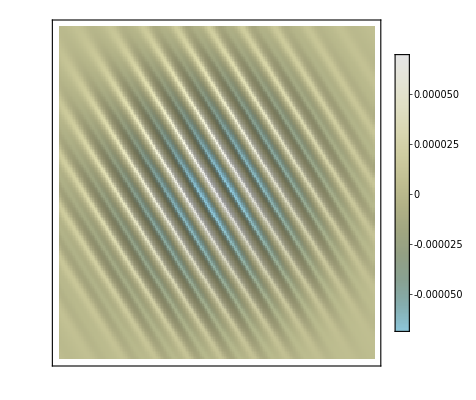

```mathematica
ReliefPlot[ GaborMatrix[100, {0.2, 0.3}], ColorFunction -> "LightTerrain", PlotLegends -> Automatic]
```

All important and less important functions of matrix algebra are also built in. Affine transforms such as rotations around a point preserve areas, so their determinant is always 1.

```mathematica
Det[RotationMatrix[45 °]]
```

1

By the way, having come this far reading the syntax of Mathematica, did you even notice the little degree constant that we applied over there to the RotationMatrix parameter to convert it to radians? All trigonometry in Mathematica operates on radians so that instead of 360 degrees, the full circle consists of 2π radians. The degree constant is just the conversion factor from degrees to radians that when concatened with the number that precedes it to perform the conversion, just gets multiplied by it.

Other classical matrix operations compute the rank, trace, eigenvalues and eigenvectors.

```mathematica
Eigenvalues[{{a, b}, {c, d}}]
Eigenvectors[{{a, b}, {c, d}}]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

Efficient exponentiation of matrices can be done with the function MatrixPower. The textbook example of this is the fastest way to compute the Fibonacci numbers with only integer arithmetic.

```mathematica
MatrixPower[{{1, 1}, {1, 0}}, 150] // MatrixForm
Fibonacci[150]
```

(16130531424904581415797907386349 | 9969216677189303386214405760200
9969216677189303386214405760200 | 6161314747715278029583501626149)

9969216677189303386214405760200

As you can see from the eigenvalues example, matrix algebra is fully symbolic, just like everything else in Mathematica and its Wolfram programming language. A couple of more examples again emphasize this important and fundamental truth.

```mathematica
{ { a+b, Sin[q+1]}, {17, E^x} } // MatrixForm
```

(a+b | Sin[1+q]
17 | ⅇ^x)

```mathematica
Inverse[%]
```

{{ⅇ^x/(a ⅇ^x+b ⅇ^x-17 Sin[1+q]),-Sin[1+q]/(a ⅇ^x+b ⅇ^x-17 Sin[1+q])},{-17/(a ⅇ^x+b ⅇ^x-17 Sin[1+q]),(a+b)/(a ⅇ^x+b ⅇ^x-17 Sin[1+q])}}

```mathematica
Inverse[%] // FullSimplify // MatrixForm
```

(a+b | Sin[1+q]
17 | ⅇ^x)

## Some applications of matrix algebra

Linear algebra and its applications is the most common use of matrices. Let us construct a simple matrix to represent a set of linear equations of three unknowns, verify that it has a unique solution by checking that its MatrixRank equals its number of rows, solve this system using LinearSolve, and verify the result using matrix multiplication.

```mathematica
myeq = { {5, -2, 7}, {8, -3, 1}, {-2, 4, 6} }
```

{{5,-2,7},{8,-3,1},{-2,4,6}}

```mathematica
MatrixRank[myeq] == First[Dimensions[myeq, 1]]
```

True

```mathematica
LinearSolve[myeq, {2, 2, 2}]
```

{37/86,45/86,11/86}

```mathematica
myeq . %
```

{2,2,2}

When a system of equations is underconstrained so that it has an infinite number of solutions, we can still use the least squares method to solve it.

```mathematica
myeq2 = { 7x + 3y == 6, -2y + 4z == 8}
```

{7 x+3 y==6,-2 y+4 z==8}

```mathematica
CoefficientArrays[myeq2, {x, y, z}]
```

{SparseArray[<2>, {2}],SparseArray[<4>, {2, 3}]}

```mathematica
Normal[%]
```

{{-6,-8},{{7,3,0},{0,-2,4}}}

```mathematica
LeastSquares[%[[2]], %[[1]]]
```

{-294/281,124/281,-500/281}

```mathematica
MapThread[(#1-> #2)&, {{x, y, z}, %}]
```

{x→-294/281,y→124/281,z→-500/281}

```mathematica
{7x + 3y, -2y + 4z} /. %
```

{-6,-8}

The function CoefficientArrays produces sparse arrays as its result. For huge matrices whose majority of elements are zeroes, as is often the case for matrices that correspond to real world problem domains where most things directly depend only on a small number of other things to keep the problem tractable to begin with, storing the matrix as a sparse array can potentially save enough memory to allow the computation to go through. The function SparseArray constructs a sparse array from the given list of substitutions from its indices to its elements. Any sparse array can always be converted to a proper matrix with all elements explicit with the polymorphic function Normal.

```mathematica
Join[Table[{i,i} -> i^2, {i, 1, 10}], Table[{i, i+2} -> i^3, {i, 1, 8}]]
```

{{1,1}→1,{2,2}→4,{3,3}→9,{4,4}→16,{5,5}→25,{6,6}→36,{7,7}→49,{8,8}→64,{9,9}→81,{10,10}→100,{1,3}→1,{2,4}→8,{3,5}→27,{4,6}→64,{5,7}→125,{6,8}→216,{7,9}→343,{8,10}→512}

```mathematica
sa = SparseArray[%]
```

SparseArray[<18>, {10, 10}]

```mathematica
MatrixForm[sa]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 9 | 0 | 27 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 16 | 0 | 64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 25 | 0 | 125 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 36 | 0 | 216 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 49 | 0 | 343 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 64 | 0 | 512
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100)

In all calculations, a sparse array behaves like a matrix. This is an important example of the powerful concepts of polymorphism and encapsulation in computer science. All of these different algorithms and calculations that operate on matrices don’t need to know exactly how the elements of some matrix are internally stored. From the point of view of these algorithms, each matrix is a black box that can tell you its dimensions and the element in any given position. This is enough for the algorithm itself, and it would work the same way not caring even if there were that proverbial three-ring circus inside that matrix performing these matrix operations.

The advantages of encapsulation and polymorphism are many. Most importantly, we don’t need to implement the same algorithm many times for all the possible different ways to express a matrix, but the exact same algorithm can work with all matrix representations that exist both now and in the future, as long as all those representations have the same public interface of the elementary matrix operations that this algorithm uses. Furthermore, encapsulation allows us to freely change the internal implementation of the system and how the data is stored there, and the outside world that uses this system does not need to change anything about the way that it deals with that system.

```mathematica
Inverse[sa] // MatrixForm
```

(1 | 0 | -1/9 | 0 | 3/25 | 0 | -15/49 | 0 | 35/27 | 0
0 | 1/4 | 0 | -1/8 | 0 | 2/9 | 0 | -3/4 | 0 | 96/25
0 | 0 | 1/9 | 0 | -3/25 | 0 | 15/49 | 0 | -35/27 | 0
0 | 0 | 0 | 1/16 | 0 | -1/9 | 0 | 3/8 | 0 | -48/25
0 | 0 | 0 | 0 | 1/25 | 0 | -5/49 | 0 | 35/81 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 0 | -3/32 | 0 | 12/25
0 | 0 | 0 | 0 | 0 | 0 | 1/49 | 0 | -7/81 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 | 0 | -2/25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/81 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/100)

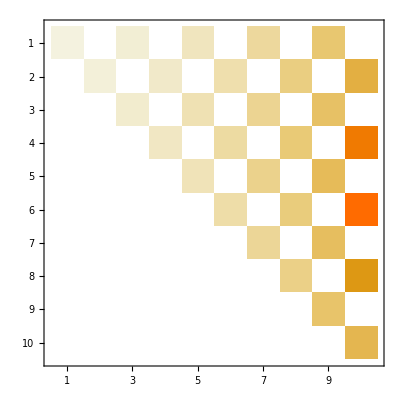

```mathematica
MatrixPlot[MatrixExp[sa]]
```

Let us create a big sparse array with some random elements filled in, and see how quickly Mathematica can handle it as a matrix.

```mathematica
size = 500;
elemrule := {RandomInteger[{1, size}], RandomInteger[{1, size}]} :> RandomInteger[{-10, +10}];
sa2 = SparseArray[Join[Table[elemrule, {i, 1, size}], Table[{i,i} -> i^2, {i, 1, size}]]]
```

SparseArray[<977>, {500, 500}]

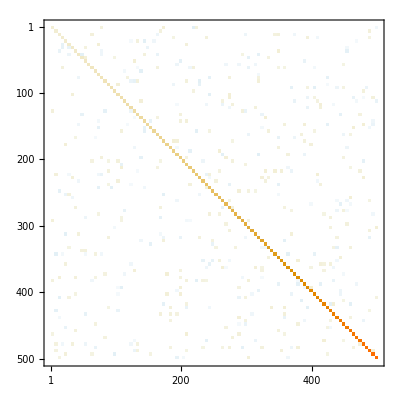

```mathematica
MatrixPlot[sa2]
```

The function Timing can be used to time the evaluation of any expression. (Why, yes, even itself. Happy to hear that you thought about that immediately.)

```mathematica
Timing[Timing[Det[sa2]]]
```

{0.05593,{0.05591,-5169214840762709760012576037176527020665185475461912441858546862660983168453838920020673386465613993710221302250505263373762292750264924663093105326851085265725745178051052247246721752539656335776571519652008513226723178448509983244245746463075526225863261158452113958376190131425020945232067077629384113779266701251499211526712633839748566245819679892178751982056808091571225913896880166460375030570981240923009231920059681447917589745960593547362075893010722725530637204756795320777016386588254340019879541780989403734542947657515261986446220995825002389438042535451823170249114485610330747388709459165902034250356384113217119910549917825798541251476189607056041484849052685387378438053026310560927936908610747347672524921068029214293742829155688502350134898975139052029315451223342732313521778341645520464440395916242068581794753961517975342100727723099006259492964485256966248599402319476013290254598431734775424006217843795978680624366159759608207174355135757639251005776780574723242945703627874050684160449449195906061861814793638037983210089375902246482475893563570228709795512565368308107247322773927627849344749460012989573990078453443878382203370558858962597818388445871823377108019149783901699882674187991324881896856373785141108099553167651662711642260847677797993018710834853772915396035029578706618630905165185723778557092120105490873775634429409360269622336668330820708732656758006670943086034236624531792776937923055207451542024491560315633084295225090534281656229095089071812026814184761929255813567540658310268374231637236957624592441667919209242157290835792511829373223009195240116104110289712140408106958428252460145624567288361743762086867263750776564432364865035958573139606162125837215313326022933583861194309976879530462148982160273853396193520016377564478105583735158583770022348465638050919087384376303683739032388007761859447933603125847001330064200430727045416301679898821954520184150478910529954452331557929360133366751251158684255270949513692990866337922648334005781607022859329018737459200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}

Well, that was quick to compute that humongous determinant on this off-the-shelf Mac desktop from the year 2011. (In the future, every computer is off-the-shelf. Somewhat later in the future, computers will become so ubiquitous that the word “computer” itself will vanish from the everyday language.)

Any simultaneous two-person zero-sum game, the most famous example of which surely being roshambo or the game of rock-paper-scissors, can be modelled with its payoff matrix whose rows represent the possible moves for the first player, and whose columns represent the possible moves for the second player. Both players choose their move simultaneously, and that entry of the payoff matrix determines the outcome. The first player tries to maximize the result, whereas the second player tries to minimize it. We can use linear algebra to compute the optimal strategy of play.

Games like this where the moves are made simultaneously, in contrast to games such as chess or poker where you always get to see what moves the other players made and then choose your response accordingly, necessarily require both players to randomize their strategies. After all, it would be very easy to play against somebody who always throws the trusty old rock! Just like for many other games, for a very wide and general definition of what constitutes a “game”, the simultaneous two-player zero-sum games must always have at least one Nash equilibrium; a set of strategies for both players so that neither player can unilaterally improve his expected result  by deviating from this strategy (and in fact, can only harm himself or at best break even), as long as the other player follows his Nash equilibrium strategy. The only time that randomization is not necessary is if the game has a saddle point, a move for each player that it does not pay to ever deviate for either player. 

For rock-paper-scissors, a simple symmetry argument shows that the equilibrium strategy is to throw each move with the same probability of 1 / 3. The difficulty of this game is that most people don’t have a proper random number generator inside their brain, and on the other hand (heh), also tend to hallucinate all sorts of patterns in where there really is only random noise, especially under the stress of winning or losing a significant sum of money on each throw. However, if we modify the familiar game slightly so that winning with scissors gives you two points instead of just one point, what does you intuition tell you about how you should adjust your strategy? (Since the modified game remains symmetric for both players, its payoff matrix will therefore still be antisymmetric, but two-player games don’t need be symmetric in general but can be partisan.)

```mathematica
mrps = { {0, -1, +1}, {+1, 0, -2}, {-1, +2, 0} };
mrps // MatrixForm
```

(0 | -1 | 1
1 | 0 | -2
-1 | 2 | 0)

To find a Nash equilibrium for the given payoff matrix, we write a set of equations based on the principle of indifference. When choosing your move, you should choose it from the probability distribution (that we are trying to solve) that has the property that every possible response of the other player has the exact same expected value for him. This way, your opponent can choose his moves any which way whatsoever and you are completely indifferent to his choices, since all his moves have the same expected value for him. (These moves may have a different variance, though, which may be significant if the game is played for stakes so high that the player’s preferences for money over the range of the session maximum win and loss are nonlinear. This does not apply to this example, though.)

Note that the Nash equilibrium stategy still cannot guarantee that you will end up with a profit within the next game or even in the next ten games, but it does give you the best average result possible in the long run. (A related well-known maxim of contract bridge says that it’s usually better to shoot for the best result possible, not for the best possible result, although that one is about understanding the limitations of your partner.) But no strategy can possibly avoid the short term fluctuations of variance in games that have an element of randomness or incomplete information, so the only way to guarantee not losing is not to play. But this is not an option if you are already stuck inside the larger game, perhaps the size of the entire physical universe so that you can no more refuse to play than you could refuse to age or breathe, and refusing to partake in some subgame is just one possible move in this larger game that you are trapped inside.

If we use symbol p_i to denote the first player’s probability of making the move number i, the opponent’s value of choosing the column j equals the sum of payoffs in that column weighted by the probabilities p_i. To compute these equilibrium probabilities, we create a list of equations that essentially say all these weighted column sums must be equal, and join these equations with another list of inequalities that say that each p_i must be between zero and one, inclusive, and they must together add to exactly one, since they are probabilities of mutually exclusive choices. These constraints are combined into one equation that is used as the constraint in minimizing the value of the weighted first column, which will then be the value of the game for the first player. Since this is a zero-sum game so that each player’s gain always exactly equals his opponent’s loss, the value of the game for each player is maximized at the point where the value of the game for his opponent is minimized.

```mathematica
strategy[payoff_] := Module[{pvars, eqns, value},
pvars = Table[Subscript[p, i], {i, 1, Dimensions[payoff][[1]]}];
eqns = Transpose[payoff] . pvars;
value = eqns[[1]];
eqns = Partition[eqns, 2, 1];
eqns = Map[(#[[1]] == #[[2]])&, eqns];
AppendTo[eqns, Apply[Plus,pvars] == 1];
eqns = Join[eqns, Map[(# ≥ 0)&, pvars]];
eqns = Join[eqns, Map[(# ≤ 1)&, pvars]];
eqns = Apply[And, eqns];
Minimize[value, eqns, pvars]
];

strategy[mrps]
```

{0,{p_1→1/2,p_2→1/4,p_3→1/4}}

To play such modified rock-paper-scissors optimally, you should choose rock with probability 1/2, and otherwise either paper or scissors with the equal probability of 1/4. Since the rules of the game are symmetric, the value of the game is still zero, assuming that both players follow their Nash equilibrium strategies.

The previous function calculates the Nash equilibrium move probabilities for the first player. To compute them for the second player, simply negate and transpose the payoff matrix to pretend that he is the first player. In this game, changing the point of view makes no difference since the matrix is antisymmetric.

```mathematica
strategy[Transpose[-mrps]]
```

{0,{p_1→1/2,p_2→1/4,p_3→1/4}}

Sharp-eyed readers with a knack for games may have noticed that following your Nash equilibrium strategy only protects you from exploitation in the sense that the opponent can choose his moves any way he likes and still can’t gain any advantage. (In fact, you could even honestly announce before the game that you will be following your Nash equilibrium strategy, and this knowledge would not help your opponent one bit!) However, following this strategy does not allow you to symmetrically exploit the opponent who, out of ignorance or negligence, deviates from his Nash equilibrium strategy. For example, if you happened to be playing against somebody who throws the rock 90% of the time, your best strategy would be to play paper 100% of the time, which would be much better against that opponent than your conservative Nash strategy. A well-known maxim in game theory about such situations notes that when you are playing against an idiot, you must also yourself play like an idiot. Once the idiot sobers up or otherwise regains his senses, you must modify your strategy accordingly, and you always have the option of returning to the Nash equilibrium any time you feel like you are being taken advantage of. 

This phenomenon becomes even more interesting in games of more than two players such as poker. When playing heads-up against a player whose overall strategy is obviously suboptimal by being too loose or too conservative, you can exploit him by playing an adapted opposite strategy that would be bad in general against an unknown opponent, but happens to be optimal against this particular opponent at this particular time. However, once a third player gets a whiff of the action and sits in, you must adapt your strategy since you are now playing against two separate opponents, so the idiotic but correct way to play against the idiot will simultaneously reveal your soft underbelly for the third player to exploit. (It is even possible that the original idiot’s moronic strategy is now the best weapon against this third player, the three of you entangled a twirling dance of increasingly eccentric strategies around the center point of the Nash equilibrium!)

Let us next take a look at what happens to these Nash equilibrium strategies if we make the win with scissors worth two points for the first player, while we make winning with rock worth ten points for the second player. What does your intuition say about the optimal strategy now? Think about it a bit before reading on.

```mathematica
mrps2 = { {0, -1, +1}, {+1, 0, -1}, {-10, +2, 0} };
mrps2 // MatrixForm
Row[{"Player one:  ", strategy[mrps2]}]
Row[{"Player two:  ", strategy[-Transpose[mrps2]]}]
```

(0 | -1 | 1
1 | 0 | -1
-10 | 2 | 0)

Player one:  {-8/39,{p_1→14/39,p_2→22/39,p_3→1/13}}

Player two:  {8/39,{p_1→5/39,p_2→7/13,p_3→1/3}}

Obviously the game heavily favours the second player, so it is not surprising that the value of the game is positive for him and negative for the first player. (However, this value is a lot closer to zero than most people might intuitively guess it to be.) Note in the answer that when you follow the Nash equilibrium strategy in such a lopsided game, you will still play your “dangerous” moves with some nonzero probability, which in here turns out to be 1/13. After all, if you never played the scissors as the first player, not wanting to donate your opponent ten points while looking like some palooka who just got an earful of cider, your opponent would never again lose even a single point by simply following the otherwise idiotic strategy of always playing paper! As it so often turns out in life in general, if you never risk anything, you risk even more.

Markov chains are another important family of problems that are easily solved using matrix algebra. A Markov chain is a system that consists of a fixed set of possible states. The system proceeds in discrete time steps so that the elements p_ij of the transition matrix are the probabilities for the system to move next to the state j if it is currently in the state i. The elements of each row of the transition matrix must therefore be positive and add up to one. It is necessary for the system to be a Markov chain that these transition probabilities are homogenous in time so that they remain the same now and always, and that the system has no memory, so that the next transition depends only on the current state, but not on where that current state was reached from.

```mathematica
tm =  {{1/3, 1/3, 1/3}, {1/2, 1/4, 1/4}, {1/8, 1/5, 1-1/8-1/5}};
tm // MatrixForm
```

(1/3 | 1/3 | 1/3
1/2 | 1/4 | 1/4
1/8 | 1/5 | 27/40)

Given this transition matrix, what proportion of its time does the system spend in each state in the long run? To solve this problem, we must find the equilibrium for the probability vector of being in each state where these probabilities don’t change by taking a single step. Since the new probabilities at time t + 1 are acquired by multiplying the probabilities at time t with the transition matrix, we can just raise this matrix to its n^th power to immediately simulate the cumulative effect of n transitions. The matrix exponentiation function MatrixPower doesn’t actually multiply the matrix by itself n - 1 times, as one might initially assume has to be done to compute the required power, but actually operates much faster because of the realization that any exponentiation a^n where n is even can be equivalently written as (a^2)^(n/2), and this way cut the number of necessary multiplications in half. The next round cuts the number in half again, and so on. This technique of binary exponentiation is very important when the matrix is large, and the idea generalizes algorithmically for other problems.

```mathematica
N[{1/3, 1/3, 1/3} . MatrixPower[tm, 1000], 10]
```

{0.2759643917,0.2492581602,0.4747774481}

This technique works assuming that our initial probability vector is nonzero for all its elements, and that in the transition matrix, it is possible to move from any state to any state (including itself) with one or more steps that have a nonzero probability. Also, the power should be large enough for the calculation to converge. But just to be on the safe side, a quick sanity check of the equilibrium probabilities.

```mathematica
Total[%]
```

1.

Using the linear algebra solver, we can write the equation that says that multiplying the equilibrium probability vector by the transition matrix produces the same equilibrium vector, and this way find the exact symbolic values for the components of this desired equilibrium vector.

```mathematica
Solve[ {x, y, z} . tm == {x, y, z} && x+y+z == 1, {x, y, z}]
```

{{x→93/337,y→84/337,z→160/337}}

```mathematica
N[%, 10]
```

{{x→0.2759643917,y→0.2492581602,z→0.4747774481}}

## Graphs and their algorithms

A matrix whose elements are zeros and ones (any list or matrix can be always converted to such form with the handy function Binarize) can in turn be converted to a graph of vertices connected by edges, by treating this matrix as the adjacency matrix of that graph. Each element of the adjacency matrix shows whether there exists an edge from the row node to the column node. When displaying a graph, Mathematica will try to produce a readable representation, but this just is inherently difficult when the graph is large and complicated.

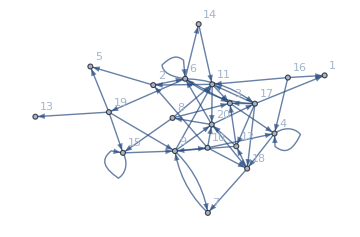

```mathematica
size = 20;
elemrule2 := {RandomInteger[{1, size}], RandomInteger[{1, size}]} :> RandomInteger[{0, 1}];
sa3 = SparseArray[Table[elemrule2, {i, 1, 5 * size}]];
g = AdjacencyGraph[sa3];
Graph[g, VertexLabels -> "Name", ImageSize -> Medium]
```

Another way to make an interesting example graph is to seed n points on the plane as vertices, and then from each point, draw an edge to each of its k nearest neighbours. (We should be careful not to count the point itself as its closest neighbour.) Note that the neighbourhood defined this way is not symmetric, since even though some point a is the nearest neighbour of some other point b, the point b does not have to be any of the k nearest neighbours of the point a. When defining a graph, the option VertexCoordinates can be used to tell Mathematica where to render each vertex. In this example, each point can serve as its own location where to draw itself.

```mathematica
nearestg[n_, k_] := Module[{pts, edges, nearest, p, p2},
pts = RandomReal[{0, 1}, {n, 2}];
nearest = Map[(Nearest[pts, #, k+1])&, pts];
edges = Flatten[Table[pts[[i]] -> nearest[[i]][[j]], {i, 1, n}, {j, 2, k+1}], 2];
Graph[pts, edges, VertexCoordinates -> pts]
];

ng = Graph[nearestg[50, 2], ImageSize -> Medium]
```

-Graphics-

Many computational problems that seemingly don’t have anything to do with graphs and their properties can still be equivalently represented as graphs whose vertices and edges somehow represent the important concepts of that problem domain. Perhaps the vertices represent individual people and edges denote their social relationships, or perhaps the vertices represent geographical locations connected by edges if they are physically adjacent. But such semantics don’t really matter, since once you have a graph, there exists a veritable plethora of different algorithms to analyze its properties and perform all sorts of computations on it independent of what we imagine those vertices and edges to represent.

The built-in GraphData knowledge base contains every graph and family of graphs important enough to have a name, and every possible graph-theoretic property of those graphs.

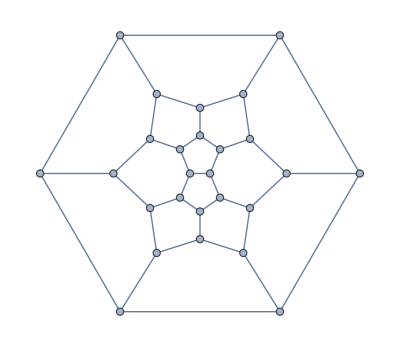

```mathematica
GraphData[{"Fullerene", {26, 1}}]
```

```mathematica
GraphData["OctahedralGraph","CliquePolynomial"]
```

(1+2 #1)^3&

A directed acyclic graph (DAG) has no directed loops so that once you leave any node, you can never get back to it by following the edges in the graph along the direction of the edges. The next example function randomdag generates a random DAG with exactly n nodes by creating an adjacency matrix whose each edge, chosen by flipping a random coin for each possible edge, always goes from lower-numbered vertex to a higher-numbered one. The algorithm could be easily modified to allow self-loops from some vertex back to itself. Whether such self-loops are meaningful in a graph to begin with, depends on the problem domain that the vertices and edges are used to model; sometimes we allow them, sometimes we don’t.

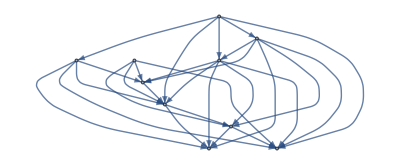

```mathematica
randomdag[n_] := Module[{adjlist, i, j},
adjlist = ConstantArray[0, {n, n}];
Do[
adjlist[[i]][[j]] = RandomInteger[{0,1}],
{i, 1, n-1}, {j, i+1, n}
];
AdjacencyGraph[adjlist]
];

randomdag[10]
```

To showcase many interesting applications of algorithms for graph searching and determining other properties of graphs, let us construct a good little playing ground graph whose vertices consist of the four-letter words of the English language, as enumerated by Mathematica’s built-in dictionary. Two words are then connected by an edge in this graph if those words can be changed to each other by changing exactly one character, for example “halt” and “hilt”, or “halt” and “hale”, but not “hale” and “hilt” that require two changes. The handy function HammingDistance can easily be used to check this, this function defined to operate polymorphically for both strings and lists.

```mathematica
words = Select[ToLowerCase[DictionaryLookup[{"English", All}]], (StringLength[#] == 4)&];
edges = {};
Do[
If[HammingDistance[words[[i]], words[[j]]] == 1,
AppendTo[edges, words[[i]] <-> words[[j]]],
Null],
{i, 1, Length[words]}, {j, i+1, Length[words]}
];
wordgraph = Graph[words, edges]
```

-Graphics-

This graph is far too big to render on screen with the word labels showing, but at least we can get an intuition about its general arachnid shape. As an idle puzzle, the reader might wish to ponder for a minute which individual words are hanging at the ends of the lone strands that emanate from the big center bulk of words heavily connected to each other either directly or indirectly over a path with at most a couple of edges. Equipped with this graph, we can now easily play the game of word ladders by looking for the shortest path between the start and goal vertices. Were this graph instead about movie actors who are connected if they have ever had a speaking part in the same movie, the game becomes the familiar dinner party amusement popularly known as “Six Degrees of Kevin Bacon”.

```mathematica
FindShortestPath[wordgraph, "warp", "duck"]
```

{warp,harp,hark,hack,huck,duck}

A connected component of a graph is a maximal subgraph whose every vertex is reachable from every other vertex in that component. In any undirected graph, every vertex belongs to exactly one connected component, and the vertices that are not connected to any other vertex form their own singleton components. How many components does the above word graph have, and what are their sizes?

```mathematica
Map[Length[#]&, ConnectedComponents[wordgraph]]
```

{3140,3,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

It looks like there is one huge component and then a whole bunch of itty bitty ones, and even a whole bunch of words that are not connected to anything and therefore form their own singleton components. Let us zoom into the singletons, doubletons and tripletons of the word graph for a better look:

```mathematica
Select[ConnectedComponents[wordgraph], (Length[#] < 4)&]
```

{{isle,idle,idly},{ogle,ogre},{ptah,utah},{fiji,fuji},{ebro,euro},{enif,enid},{aura,agra},{it'd,it's},{cebu,zebu},{oahu},{kiwi},{ebbs},{idol},{ague},{kuhn},{hahn},{ammo},{ciao},{guru},{skua},{xmas},{zuni},{usmc},{hiya},{suzy},{envy},{ncaa},{aqua},{ibex},{sgml},{iffy},{igor},{okay},{iyar},{void},{ohsa},{apse},{yegg},{épée},{semi},{agni},{eton},{yeti},{sexy},{elul},{agog},{espy},{bozo},{i've},{oslo},{urge},{goya},{fnma},{usaf},{html},{yacc},{ohio},{lvov},{inge},{omsk},{ankh},{afro},{echo},{okra},{skye},{epee},{amur},{fahd},{obey},{jehu},{egad},{upon},{hymn},{rely},{ucla},{hajj},{ayah},{audi},{izod},{baez},{ahoy},{imam},{ainu},{sync},{http},{sufi},{tupi},{piaf},{asap},{eyck},{nazi},{zibo},{once},{i'll},{kohl},{ezra},{isbn},{ufos},{azov},{xian},{kroc},{onyx},{ruhr},{ovum},{styx},{ugly},{meow},{lsat},{urdu},{rsvp},{esau},{expo},{ecru},{rabi},{ebay},{ulna}}

On the opposite side, what words in this graph have the largest number of immediate neighbours?

```mathematica
GraphHub[wordgraph]
```

{bars,mars}

```mathematica
VertexDegree[wordgraph, "bars"]
```

31

What is the largest clique within words, that is, a set of vertices that all are directly connected to each other with an edge?

```mathematica
FindClique[wordgraph]
```

{{bays,cays,days,fays,gays,hays,jays,lays,mays,nays,pays,rays,says,ways}}

Built-in functions that extract some small part of a possibly much larger graph include the ability to extract the immediate neighbourhood of the given vertex up to some distance from that vertex. This gives us a nice small graph that we can use to illustrate all sorts of structural algorithms on graphs.

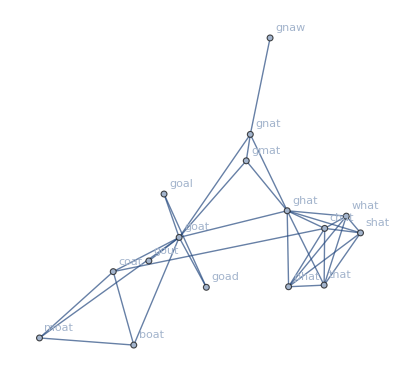

```mathematica
gnatG = NeighborhoodGraph[wordgraph, "gnat", 2, VertexLabels -> "Name"]
```

A vertex cover is a subset of vertices so that every vertex is either in this set or is directly connected to at least one vertex in it. When we this function and all others that return a set of vertices or edges as their solution, the function HighlightGraph can be used to highlight the solution inside the original graph.

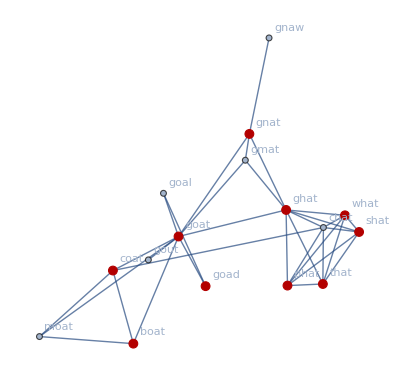

```mathematica
HighlightGraph[gnatG, FindVertexCover[gnatG], VertexSize -> 0.4]
```

Independent set is a very similar problem, asking you to find a maximal subset of vertices so that no two vertices in that set are directly connected to each other. In fact, this problem turns out to be exactly as easy or as difficult as the previous clique problem, since the vertices of the independent set of some graph are precisely the vertices of the clique in its complement graph, and vice versa. But so it is by definition with all these NP-complete problems: an instance of any one of them can be converted to an equivalent instance of any other one of them.

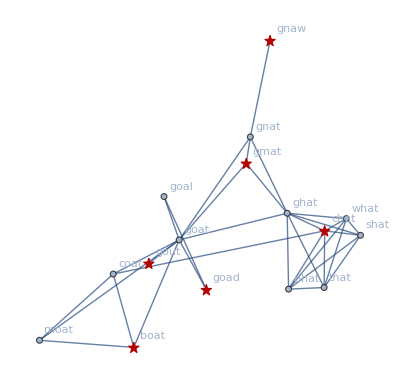

```mathematica
HighlightGraph[gnatG, FindIndependentVertexSet[gnatG], VertexSize -> 0.4,VertexShapeFunction -> "Star"]
```

The powerful graph traversal functions BreadthFirstScan and DepthFirstScan can be used to traverse all vertices of the graph that are reachable from the given start vertex, visiting these reachable vertices along the way in guaranteed “breadth-first” or “depth-first” order from which other mathematical properties of the graph can then be ascertained. In both vertex scanning functions, you can perform an arbitrary action for each vertex at the time that is discovered, visited by the search, or a couple of other possibilities. This versatility can be used to write graph-theoretical functions that compute all sorts interesting properties of the graph. For example, suppose we wish to calculate the diameter of the graph, the distance between two antipodal vertices that are as far away from each other as possible even if we took the shortest possible path between these two vertices. Two such vertices can be found using two consecutive runs of breadth first search. The first run can start from any vertex in the component in which we want to do this search, but the second run must start from the last vertex that was visited by the first run.

```mathematica
BreadthFirstScan[gnatG, "gnat", {"PrevisitVertex" -> ((last = #)&)}];
BreadthFirstScan[gnatG, last, {"PrevisitVertex" -> ((last2 = #)&)}];
FindShortestPath[gnatG, last, last2]
```

{moat,goat,gnat,gnaw}

Since this scan takes place in linear time with respect to number of vertices and edges, we can easily do it even for the entire word graph.

```mathematica
BreadthFirstScan[wordgraph, "bars", {"PrevisitVertex" -> ((last = #)&)}];
BreadthFirstScan[wordgraph, last, {"PrevisitVertex" -> ((last2 = #)&)}];
FindShortestPath[wordgraph, last, last2]
```

{edge,edgy,eddy,edda,edna,erna,erma,elma,alma,alms,ales,oles,odes,odis,obis,obit,omit,emit,emir,ymir}

Using an association to store all distances from the given start word, we next simultaneously compute the distance of each word from the starting word “glue”. An association is an efficient data structure that can be used to store rules of the form (key → value) and can then later be used to look up the value for the given key very quickly even if the association contains millions of keys. This type of dictionary data structure, internally implemented as a hash table, can be quite a powerhouse in many algorithms for heavy computational problems.

```mathematica
distances = Association[];
BreadthFirstScan[wordgraph, "glue", {"DiscoverVertex" -> ((AssociateTo[distances, #1 -> #3])&)}];
distances[["drop"]]
```

6

We can use the shortest path function to verify that the above result is correct.

```mathematica
FindShortestPath[wordgraph, "glue", "drop"]
```

{glue,flue,floe,flop,clop,crop,drop}

Associations can also come useful in memoizing the results of recursive functions that suffer from repeated subproblems. Of course you could let Mathematica do the memoization for you using the pattern memoization idiom, but when you maintain your own association for the subproblem results that you have already computed, you can easily modify or prune this set later should you run low on memory. As a simple example, consider the problem where you are standing at the point (x, y) of the integer grid, the coordinates x and y both being nonnegative integers. Your task is to get to the origin (0, 0) so that in each step, you can move either left or down by one unit, but you can never move right or up. How many different paths are now possible for you to take that lead you to the origin?

A moment’s thinking tells us that there are precisely two kinds of legal paths leading from (x, y) to the origin; those that start with a left step, and those that start with a down step. Since these possibilities are mutually exclusive, the asked quantity is the sum of the recursively computed number of paths that start each way. Since this recursion branches to two directions each time and would take an exponential time to gather up the repeated results, we memoize all results that have already been computed so that we don’t need to compute them again from scratch every next time that we encounter them again. The main difficulty here is coming up with suitable association keys; for this purpose, we make up a new symbol σ_xy to serve as the key for the subproblem (x, y). We can’t use a list {x, y} as the key, because the function Lookup would then try to perform a key-value lookup for both of its components x and y separately!

```mathematica
pathassoc = Association[];
paths[0,y_]  =1;
paths[x_, 0] = 1;
paths[x_, y_] := Module[{result},
If[KeyExistsQ[pathassoc, Subscript[σ, x, y]],
result = Lookup[pathassoc, Subscript[σ, x, y]],
result = paths[x-1, y] + paths[x, y-1];
AssociateTo[pathassoc, Subscript[σ, x, y]-> result];
];
result
] /; x>0 && y > 0
paths[50, 50]
```

100891344545564193334812497256

This particular problem also happens to allow a much simpler combinatorial solution once you realize that each path must consist of exactly x + y steps, of which exactly x are left steps somehow interleaved with y down steps. Therefore, the total number of paths equals the number of ways that you can choose a subset of x positions from x + y possible positions. This in turn is a simple application of the function Binomial.

```mathematica
pathscomb[x_, y_] := Binomial[x+y, x];
pathscomb[50, 50]
```

100891344545564193334812497256

So far, all edges in the graphs have been equally nondescript, containing no other information than the two vertices that they connect. If we give each edge a numerical weight, a whole new family of interesting graph computations emerges from its cocoon.

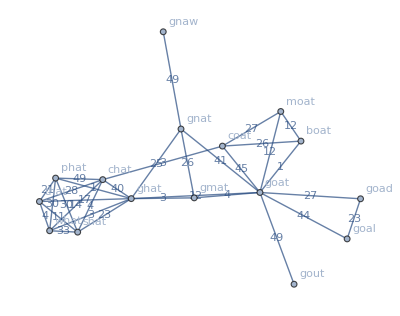

```mathematica
gnatW = Graph[VertexList[gnatG], EdgeList[gnatG], VertexLabels -> "Name", EdgeLabels -> Placed["EdgeWeight", "Middle"], EdgeWeight -> Table[RandomInteger[{1, 50}], {Length[EdgeList[gnatG]]}]]
```

Once the weights have been given, finding the shortest path in a weighted graph takes these weights into consideration. You can also specify the shortest-path algorithm used internally by this function, if you wish.

```mathematica
FindShortestPath[gnatW, "goal", "what", Method -> "Dijkstra"]
```

{goal,goat,gmat,ghat,what}

The minimum spanning tree problem asks you to find a tree-shaped subset of edges that still keeps the graph connected so that you can get from any vertex to every other by following the edges of the spanning tree, and whose total weight is the smallest possible. Several algorithms are known for this problem, most famously the algorithms of Kruskal and Prim.

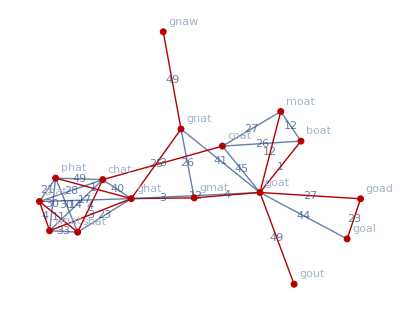

```mathematica
HighlightGraph[gnatW,FindSpanningTree[gnatW, Method -> "Prim"]]
```

Mathematica has a very powerful function Import that can read and process pretty much any standard type of file, fetched either from the file system or from the World Wide Web, and extract the desired data elements from it to computable form. To demonstrate its use, the next function crawls the English-language Wikipedia from the given starting URL using the discipline of breadth-first search traversal to the hyperlinks to other articles in the English-language Wikipedia. The logic of breadth-first search, or for that matter any graph search, is quite easy to implement yourself, even if you didn’t have the function BreadthFirstScan available. The search algorithm keeps the discovered vertices in frontier list of vertices waiting to be processed, from which it then repeatedly takes out the oldest element. (Taking out the newest element would implement depth-first search.) The links that this element contains are added to the graph as edges and followed to their target URL:s, of which those that have not been discovered so far are added to the frontier to wait for their turn. The search continues until the frontier becomes empty, in which case the entire reachable subset of graph has been traversed, or the count of vertices reaches the given limit of vertices to process. The graph will still end up containing the vertices in the frontier, but since they have not yet been processed, there are no edges emanating from them.

```mathematica
name[url_] := Last[StringSplit[url, "/"]];

wikipediacrawl[start_, maxurls_, maxlinks_] := Module[{count = 0, urls, vertices, edges, frontier, u, v, discard, links, reject},
reject = RegularExpression[".+(File:|Wikipedia:|Talk:|Special:|Portal:|Help:|Template:|Template_talk:).+"
];
urls = {start};
vertices = {name[start]};
edges = {};
frontier = {start};
While[count < maxurls && Length[frontier] > 0,
count++;
u = First[frontier];
frontier = Rest[frontier];
links = Import[u, "Hyperlinks"];
links = Select[links, (StringMatchQ[#,"http://en.wikipedia.org/wiki/" ~~ __])&];
links = Select[links, (!StringMatchQ[#, __ ~~ "(disambiguation)"])&];
links = Select[links, (!StringMatchQ[#, reject])&];
If[Length[links] > maxlinks,
links = Take[links, maxlinks], Null
];
Do[
AppendTo[edges, name[u] -> name[v]];
If[MemberQ[urls, v],
Null,
AppendTo[frontier, v]; AppendTo[urls, v]]; AppendTo[vertices, name[v]]
,{v, links}
];
];
Graph[vertices, edges, VertexLabels -> "Name"]
];
```

To ensure that only proper articles of the English-language Wikipedia are added to the graph, the hyperlinks that are imported inside the loop are immediately filtered so that only those that point to the English-language Wikipedia are kept, after which we filter out those that match the regular expression that matches the file name prefixes internally used in Wikipedia to refer to pages that are not proper articles. Regular expressions are a very powerful way to define patterns that can be used to match strings. The prefix .+ means “any character one or more times”, and the vertical bar | is used to express alternatives.

Starting from Kevin Bacon, the next expression produces a graph that processes the first ten vertices before terminating. To keep the frontier small and the graph from becoming a mess of edges, we follow only the first five links from each page.

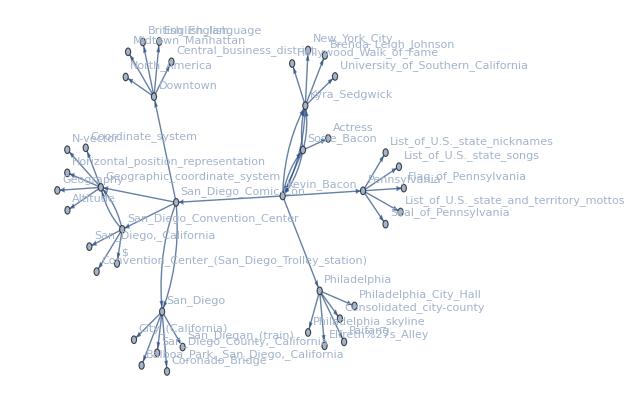

```mathematica
bacongraph = wikipediacrawl["http://en.wikipedia.org/wiki/Kevin_Bacon", 10, 5]
```

If we follow only the first two links on each page, where do we end up? To all sorts of places! Like everything else in Wikipedia, Kevin Bacon is closely connected to concepts from geodesy to the flag of Sweden and Benjamin Franklin. Many of these connections are just spurious in that they represent confusion warnings of other similarly named concepts and accidental choices of the Wikipedia sidebar images.

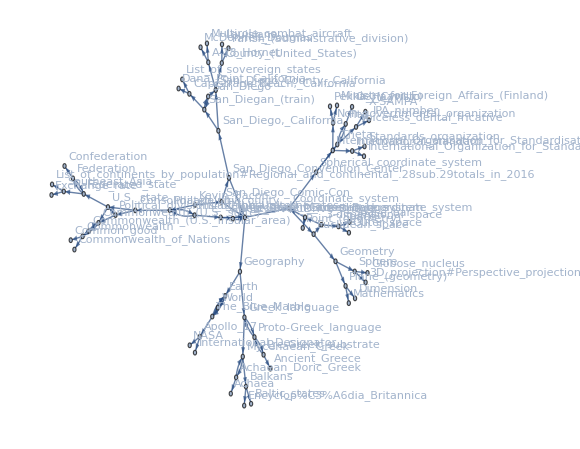

```mathematica
wikipediacrawl["http://en.wikipedia.org/wiki/Kevin_Bacon", 50, 2]
```

Following all links on each page would make the graph quickly puff up.

```mathematica
Graph[wikipediacrawl["http://en.wikipedia.org/wiki/Banana", 10, Infinity], VertexLabels -> None, GraphStyle -> "LargeNetwork"]
```

-Graphics-

In the next example, we turn lovely Lena into a graph so that the pixels of the image become vertices of the graph, and each vertex is connected with an edge to the vertices that correspond to its four adjacent pixels. We make this graph weighted so that the weight of each edge depends on the brightness difference of the two pixels. In the graph generated thus, we can then look for the shortest path between two pixels, and plot those pixels on the original image. Since the lists of vertices and edges become quite long, they are better generated in linear time with Sow and Reap than in quadratic time by appending each new vertex and edge at the time, necessitating the creation of a identical copy of the list in which the new element is appended. (Also note the use of the function Clip to limit the value between the desired range of minimum and maximum.)

```mathematica
lena = ImageResize[ExampleData[{"TestImage","Lena"}], 128];
graylena = ColorConvert[lena, "Grayscale"];
{w, h} = ImageDimensions[lena];
vertices = Flatten[Table[{Floor[i/w]+1, Mod[i, w]+1}, {i, 0, w*h-1}], {1}];
inside[{x_, y_}] := {Clip[x, {1, w}], Clip[y,{1, h}]};
dirs = { {+1, 0}, {0, +1}, {-1, 0}, {0, -1} };
{dummy, {edges}} = Reap[
Do[
Sow[{x, y} -> inside[{x,y} + d]],
{x, 1, w}, {y, 1, h}, {d, dirs}
]
];
{dummy, {edgeweights}} = Reap[
Do[
Sow[0.1 + Abs[ImageValue[graylena, {x, y}] - ImageValue[graylena,inside[{x,y} + d]]]],
{x, 1, w}, {y, 1, h}, {d, dirs}
]
];
lenag = Graph[vertices, edges, EdgeWeight -> edgeweights, VertexCoordinates ->  vertices];
sg = FindShortestPath[lenag, {10,108}, {108, 10}];
Do[
lena = ReplacePixelValue[lena, p -> RGBColor[1,1,1]],
{p, sg}
];
ImageResize[lena, 256]
```

-Graphics-